```mathematica
(* priklad c. 1 *)

rules=Flatten[{
{MΩ->10^6 Ω,kΩ->10^3 Ω,Ω->10^0 Ω,mΩ->10^-3 Ω,μΩ->10^-6 Ω,nΩ->10^-9 Ω},
{MH->10^6 H,kH->10^3 H,H->10^0 H,mH->10^-3 H,μH->10^-6 H,nH->10^-9 H},
{ML->10^6 L,kL->10^3 L,L->10^0 L,mL->10^-3 L,μL->10^-6 L,nL->10^-9 L}}];

R1=10 kΩ/.rules
R2=20 MΩ/.rules
C1=10 mH/.rules
C2=100 μH/.rules
L1=5 mH/.rules
L2=3 μH/.rules
u12/R1+u23/R2=C1*u3'-C2*u4'+i1+i2/.rules
u1=L1*i1'/.rules
u2=L2*i2'/.rules
```

10000 Ω

20000000 Ω

H/100

H/10000

H/200

(3 H)/1000000

i1+i2+(-(H u4)/10000+(H u3')/100)'

(H i1')/200

(3 H i2')/1000000

```mathematica
(* priklad c. 2 *)
```

x∈Integers&&x≥220.

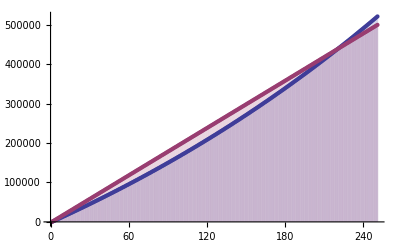

```mathematica
vklad=1500;
prispevek=500;
rocniUrok=0.03;
mesicniUrok=rocniUrok/12;
duchodove[x_]:=x*(vklad+prispevek);
sporiciM[x_]:=(x+vklad)*(1+mesicniUrok);
sporici[x_]:=Nest[sporiciM,0,Abs[IntegerPart[x]]];
sporici2[x_]:=Sum[vklad*(1+mesicniUrok)^i,{i,x}];

Off[Reduce::ratnz]

Reduce[sporici2[x]>duchodove[x]&&x>0,{x},Integers]

sporiciT=NestList[sporiciM,0,250];
duchodoveT=Table[(x-1)*(vklad+prispevek),{x,251}];

ListPlot[{sporiciT,duchodoveT},Filling->Axis]
```

```mathematica
.
```

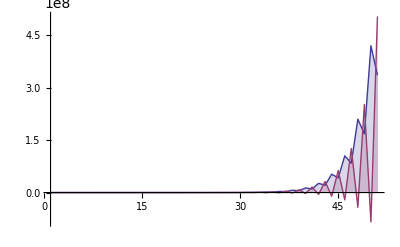

```mathematica
(* priklad c. 3 *)

funkce[x_]:={{x}[[1,1]]+{x}[[1,2]],{x}[[1,1]]-{x}[[1,2]]};
vysledek=NestList[funkce,{10,15},50];
ListLinePlot[{vysledek[[All,1]],vysledek[[All,2]]},Filling->Axis,PlotRange->All]
```

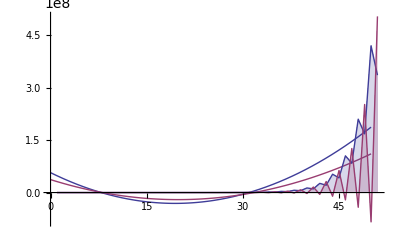

{{x→7.57126},{x→29.7061}}

```mathematica
parabola1= Fit[vysledek[[All,1]], {1,x,x^2}, x];
parabola2= Fit[vysledek[[All,2]], {1,x,x^2}, x];
Show[Plot[{parabola1,parabola2},{x,0,50}],ListLinePlot[{vysledek[[All,1]],vysledek[[All,2]]},Filling->Axis,PlotRange->All],PlotRange->All]
Solve[parabola1==parabola2,x]
```